# Lab 8 William Keilsohn Section #32 May 8 2014

1) Consider the function f(x)=xe^-x. Find the Taylor series polynomials of degree 5,10, and 15 that approximate f(x). Create graphs comparing f(x) to these approximations. If P15(x) denotes the Taylor series polynomial of degree 15, compare the values of the two given integrals.

```mathematica
Quit[]
```

```mathematica
f[x_]=x*Exp[-x]
```

ⅇ^-x x

```mathematica
P5[x_]=Series[f[x],{x,0,5}]//Normal
```

x-x^2+x^3/2-x^4/6+x^5/24

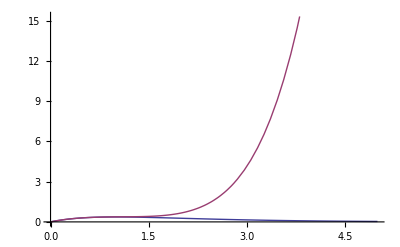

```mathematica
Plot[{f[x],P5[x]},{x,0,5}]
```

```mathematica
P10[x_]=Series[f[x],{x,0,10}]//Normal
```

x-x^2+x^3/2-x^4/6+x^5/24-x^6/120+x^7/720-x^8/5040+x^9/40320-x^10/362880

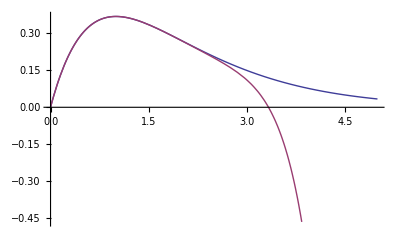

```mathematica
Plot[{f[x],P10[x]},{x,0,5}]
```

```mathematica
P15[x_]=Series[f[x],{x,0,15}]//Normal
```

x-x^2+x^3/2-x^4/6+x^5/24-x^6/120+x^7/720-x^8/5040+x^9/40320-x^10/362880+x^11/3628800-x^12/39916800+x^13/479001600-x^14/6227020800+x^15/87178291200

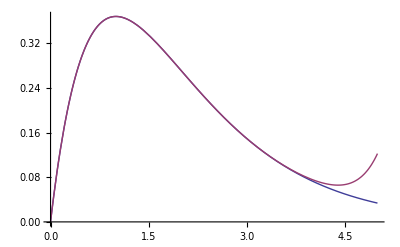

```mathematica
Plot[{f[x],P15[x]},{x,0,5}]
```

```mathematica
Integrate[f[x],{x,0,3}]
```

1-4/ⅇ^3

```mathematica
N[1-4/ⅇ^3]
```

0.800852

```mathematica
Integrate[P15[x],{x,0,3}]
```

469084167/585728000

```mathematica
N[469084167/585728000]
```

0.800857

Based on the graphs above P15 is the closest Taylor Series approximation when compared to Taylor Series of degree 5 and 10. 

Based on the numerical values produced by the integrals from 0 to 3 the  area under the curve of the Taylor series aproximation of degree 15 is larger than the area under the curve of f(x) by about 0.000002 square units. Or in other words the Integral from 0 to 3 is larger for P15(x) than f(x).

2)Consider the function f(x)= (sinx)/x. Find Taylor series polynomials of degrees 8 and 12 that approximate the function f(x). Create graphs comparing f(x) to these approximations. If P12(x) denotes the Taylor polynomial of degree 12, compare the values of the two given integrals.

```mathematica
Quit[]
```

```mathematica
f[x_]=(Sin[x])/x
```

Sin[x]/x

```mathematica
P8[x_]=Series[f[x],{x,0,8}]//Normal
```

1-x^2/6+x^4/120-x^6/5040+x^8/362880

```mathematica
P12[x_]=Series[f[x],{x,0,12}]//Normal
```

1-x^2/6+x^4/120-x^6/5040+x^8/362880-x^10/39916800+x^12/6227020800

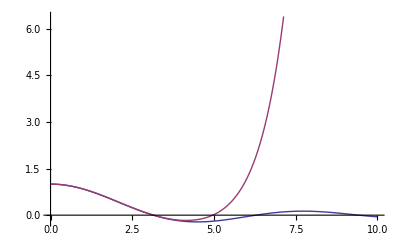

```mathematica
Plot[{f[x],P8[x]},{x,0,10}]
```

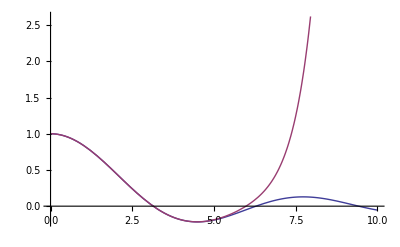

```mathematica
Plot[{f[x],P12[x]},{x,0,10}]
```

Based on the graphs above, P12 is a closer aproximation over the given interval than P8.

```mathematica
Integrate[P12[x],{x,0,5}]
```

1160407880855/747989738496

```mathematica
N[1160407880855/747989738496]
```

1.55137

```mathematica
N[Integrate[f[x],{x,0,5}]]
```

1.54993

Based on the above integral it can be concluded that the Taylor Series polynomial approximation of degree 12 has large values and thus has a greater area under the curve than f(x).

3) In the same plot, display the following curves.

```mathematica
Quit[]
```

```mathematica
x1[t_]=2*Cos[t]+Cos[2*t]
y1[t_]=2*Sin[t]-Sin[2*t]
x2[t_]=3*Cos[t]-Cos[9*t]
y2[t_]=3*Sin[t]-Sin[9*t]
```

2 Cos[t]+Cos[2 t]

2 Sin[t]-Sin[2 t]

3 Cos[t]-Cos[9 t]

3 Sin[t]-Sin[9 t]

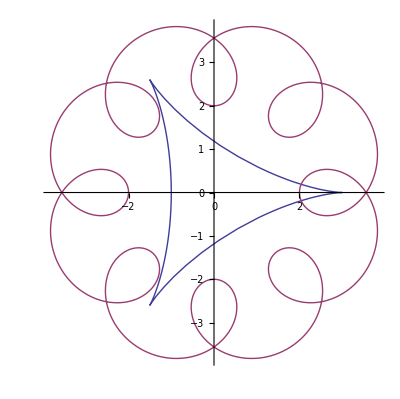

```mathematica
ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]}},{t,0,2*Pi}]
```

4) In the same plot as eachother add the plots for r(Theta).

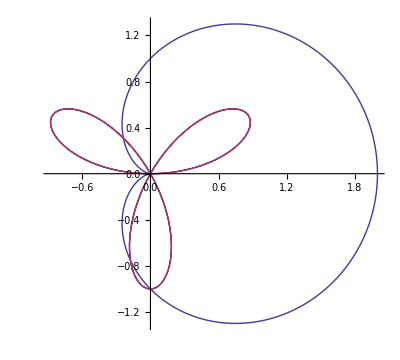

```mathematica
PolarPlot[{Cos[x]-1,Sin[3*x]},{x,0,2*Pi}]
```

5)Consider the rose r(Theta)=Sin(3Theta). Plot its graph and find its derivative.

```mathematica
?Theta
```

Information::notfound: Symbol "Theta" not found.

```mathematica
r[θ_]=Sin[3*θ]
```

Sin[3 θ]

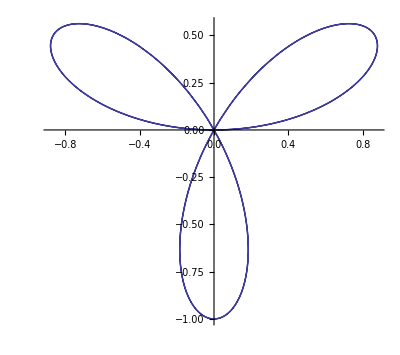

```mathematica
PolarPlot[r[θ],{θ,0,2*Pi}]
```

```mathematica
x[θ_]=r[θ]*Cos[θ]
y[θ_]=r[θ]*Sin[θ]
```

Cos[θ] Sin[3 θ]

Sin[θ] Sin[3 θ]

```mathematica
m[θ_]=(y'[θ])/(x'[θ])
```

(3 Cos[3 θ] Sin[θ]+Cos[θ] Sin[3 θ])/(3 Cos[θ] Cos[3 θ]-Sin[θ] Sin[3 θ])

```mathematica
m[Pi/4]
```

1/2

Based on the above calculations we can conclude that the slope of the tangent line at Theta=Pi/4 is 1/2.